# Image detection

```mathematica
i=-Graphics-;
b = Binarize[i,{0,0.9}]
```

-Graphics-

```mathematica
pores = ComponentMeasurements[b,{"Centroid","EquivalentDiskRadius"},#AdjacentBorderCount==0 && 50 < #Area < 1200 &]
```

{2→{{2516.23,5667.71},5.23208},3→{{2497.94,5655.78},4.98279},7→{{2086.26,5633.26},4.18414},13→{{2498.91,5602.95},8.09764},18→{{2491.04,5573.19},13.3869},19→{{2206.49,5566.56},9.57461},20→{{2574.26,5542.47},16.7175},23→{{2519.12,5549.83},4.40646},29→{{2616.61,5532.76},4.14593},39→{{2302.56,5494.32},17.3161},48→{{3604.92,5497.99},6.0239},53→{{2339.3,5487.76},7.18096},55→{{2624.5,5489.67},6.25717},58→{{1567.13,5484.15},7.48482},65→{{2271.24,5456.8},6.86366},70→{{1304.11,5449.21},4.95074},73→{{3627.77,5444.2},10.1554},76→{{2229.02,5444.99},4.95074},86→{{2294.02,5432.24},4.54864},89→{{3066.17,5435.19},4.02912},91→{{2049.35,5414.83},13.3631},92→{{2084.58,5426.48},4.33362},94→{{2553.57,5412.53},7.00141},95→{{2466.34,5424.46},8.33016},98→{{2531.82,5412.74},9.47435},104→{{1921.99,5398.47},11.1132},110→{{2304.48,5393.45},5.67004},113→{{1132.81,5384.43},4.40646},118→{{1874.5,5379.21},5.23208},123→{{2267.23,5379.09},5.41152},127→{{1270.1,5365.06},6.84044},129→{{3567.31,5369.81},6.77028},130→{{3836.84,5369.88},5.35237},135→{{2558.21,5364.21},3.94933},136→{{3912.23,5359.34},7.18096},145→{{3692.05,5342.67},12.7287},147→{{2172.12,5350.02},4.29674},148→{{2190.67,5348.68},5.6419},164→{{2553.84,5328.88},6.74673},166→{{2172.05,5333.65},4.10736},170→{{1776.3,5330.93},4.85334},173→{{1814.77,5325.45},6.79374},174→{{3761.51,5303.37},13.8198},176→{{1354.74,5321.42},5.89031},179→{{3165.59,5313.85},10.3571},181→{{2220.78,5324.62},9.72307},185→{{1663.41,5310.63},8.51908},186→{{4031.57,5310.83},6.93288},188→{{1605.57,5305.24},14.2395},193→{{4055.7,5308.91},5.78122},200→{{3704.14,5297.78},8.68559},210→{{2526.08,5291.3},8.70389},211→{{3538.93,5284.88},12.3608},213→{{3059.66,5291.78},7.99877},219→{{2831.99,5290.57},4.33362},221→{{2943.15,5286.96},9.04465},222→{{1214.86,5267.12},15.6251},224→{{2347.44,5285.43},4.61809},225→{{1439.08,5283.91},5.29257},228→{{3277.66,5290.73},8.48163},229→{{4364.43,5264.17},13.8428},234→{{3733.56,5271.51},5.47002},236→{{1707.2,5271.5},4.37019},239→{{2574.05,5255.72},11.6857},240→{{3866.57,5268.07},9.47435},244→{{3510.63,5266.19},4.72035},246→{{1838.47,5261.26},9.54131},247→{{3151.47,5263.84},5.44085},252→{{2948.01,5248.68},10.2335},257→{{1488.23,5256.71},4.22201},259→{{3510.85,5255.95},4.68651},261→{{3949.62,5247.61},10.8963},269→{{3012.57,5238.42},7.15876},276→{{2815.06,5232.3},4.18414},286→{{2572.09,5220.64},4.5835},288→{{2198.19,5219.45},7.89865},290→{{2907.58,5222.98},3.98942},299→{{3391.51,5173.71},16.9633},303→{{2456.45,5192.6},7.24715},304→{{4275.09,5192.18},4.47812},306→{{2633.3,5192.27},5.07771},324→{{3342.27,5162.21},13.564},325→{{3774.21,5157.03},9.2534},326→{{2807.88,5162.4},3.98942},327→{{4191.78,5154.76},11.5487},328→{{806.382,5145.62},7.15876},331→{{1187.27,5148.73},7.0241},334→{{1359.27,5141.63},6.90988},336→{{3752.97,5135.7},7.15876},342→{{4404.25,5130.7},4.40646},351→{{1373.6,5119.06},4.98279},356→{{3875.19,5101.74},5.04627},359→{{1405.03,5098.25},7.29094},361→{{831.148,5085.66},18.9403},366→{{3697.18,5096.36},4.25954},370→{{3683.72,5081.92},7.89865},372→{{2614.79,5075.29},6.20609},376→{{1939.84,5047.07},14.9484},379→{{1513.03,5067.21},9.23618},386→{{924.111,5049.18},11.5899},387→{{1336.64,5044.43},9.27058},389→{{1306.67,5048.88},7.59039},390→{{1551.43,5046.65},4.65243},400→{{3627.34,5027.76},3.98942},401→{{764.083,5023.43},8.55636},403→{{975.188,5008.44},11.1561},408→{{2524.18,5011.57},5.29257},411→{{1334.53,4978.67},17.4808},414→{{2475.77,4992.4},10.9691},415→{{2967.62,5000.24},5.17088},420→{{645.097,4982.81},9.77205},426→{{720.289,4982.29},6.50655},435→{{1242.98,4965.58},9.82079},440→{{4573.94,4960.81},4.06843},444→{{2290.59,4948.37},4.61809},445→{{787.191,4942.92},5.07771},447→{{701.277,4934.62},10.8083},448→{{1318.76,4934.74},5.83602},450→{{763.838,4924.58},6.93288},451→{{1197.96,4914.31},9.27058},452→{{2779.45,4918.13},4.51352},457→{{1411.08,4905.09},8.53774},458→{{1168.06,4883.21},15.5126},459→{{2352.65,4876.69},16.888},462→{{558.97,4880.33},4.5835},465→{{607.391,4862.9},8.01864},467→{{2110.27,4858.44},8.40624},469→{{4587.62,4859.82},3.98942},470→{{2353.23,4858.08},4.18414},483→{{2078.6,4780.43},6.23168},485→{{3924.67,4748.28},17.7787},487→{{4025.95,4755.8},5.89031},488→{{4084.92,4748.67},10.1083},494→{{533.796,4733.08},6.55529},496→{{1417.22,4705.99},5.29257},498→{{4346.2,4683.46},7.26907},499→{{1532.88,4696.92},6.93288},511→{{1353.86,4646.39},9.339},514→{{1135.25,4633.59},5.55662},528→{{4525.31,4588.5},4.95074},529→{{3447.73,4579.3},7.85825},533→{{1520.12,4561.81},4.18414},536→{{4560.52,4549.43},13.8313},539→{{4296.21,4544.54},6.86366},542→{{4260.98,4527.},12.603},543→{{1753.01,4527.22},6.25717},551→{{3526.45,4488.27},10.555},553→{{4431.9,4492.67},4.54864},554→{{685.332,4488.61},6.45744},561→{{2003.55,4454.18},7.91878},563→{{4513.47,4451.95},5.86323},565→{{4428.92,4429.38},9.65737},566→{{4519.83,4432.76},9.2534},583→{{607.327,4386.36},7.91878},584→{{4373.49,4394.98},7.71518},588→{{4468.44,4376.53},15.6353},594→{{2512.9,4344.71},7.11416},595→{{4449.32,4327.77},10.7641},598→{{4418.99,4319.94},5.32255},605→{{1178.43,4302.03},4.33362},606→{{4570.12,4292.47},5.38203},611→{{2911.21,4280.57},4.18414},613→{{4314.89,4274.74},4.88603},617→{{588.993,4255.08},4.68651},628→{{747.698,4214.35},8.21472},629→{{535.132,4198.36},6.77028},631→{{1311.12,4201.79},4.06843},640→{{4251.19,4167.41},9.82079},644→{{783.312,4158.5},4.68651},659→{{1126.25,4087.02},5.14001},660→{{2092.26,4063.55},7.75632},662→{{689.717,4049.13},4.37019},664→{{4368.97,4036.54},6.33301},671→{{495.541,3996.91},3.94933},673→{{580.521,3988.68},5.47002},676→{{527.207,3975.66},11.6993},691→{{3629.12,3852.43},4.65243},696→{{3047.43,3826.24},5.23208},701→{{640.826,3792.43},5.23208},713→{{1317.,3765.66},5.67004},718→{{4461.87,3712.1},7.52723},731→{{806.34,3695.74},3.98942},734→{{3976.27,3667.61},8.66724},738→{{4523.98,3573.78},4.14593},739→{{960.58,3562.88},12.1137},750→{{1466.98,3461.38},4.22201},751→{{532.915,3458.18},4.10736},753→{{1011.83,3444.64},5.49904},764→{{738.748,3372.05},8.84897},767→{{858.408,3359.14},5.58519},781→{{832.318,3330.63},5.91727},784→{{830.312,3294.2},7.79726},788→{{1057.29,3285.63},6.10264},811→{{4500.83,3136.93},5.01463},815→{{4105.44,3091.84},11.0702},817→{{4041.06,3088.15},6.69938},825→{{1397.21,3037.81},5.6419},834→{{4394.47,2984.24},8.25338},837→{{522.077,2945.88},14.116},839→{{682.11,2945.69},7.11416},847→{{524.943,2920.35},5.29257},851→{{4599.79,2896.57},5.17088},856→{{4563.04,2865.52},18.0276},857→{{493.077,2882.54},4.98279},863→{{494.465,2871.29},5.99742},875→{{498.531,2822.02},4.51352},876→{{1210.62,2802.84},16.2835},879→{{1304.6,2793.12},4.75395},885→{{446.395,2772.41},4.25954},887→{{1105.91,2765.64},4.33362},890→{{3276.19,2757.32},4.44243},894→{{524.463,2728.58},16.7556},897→{{4266.03,2708.58},17.8858},903→{{4447.04,2691.5},6.53097},904→{{4311.78,2686.37},8.84897},905→{{1133.68,2684.34},5.14001},916→{{4422.48,2637.02},12.4889},917→{{4609.48,2633.99},10.8671},919→{{474.043,2621.83},6.40796},923→{{606.316,2611.81},3.94933},927→{{560.833,2578.8},12.2443},935→{{3591.72,2568.54},6.50655},938→{{1361.39,2534.33},8.70389},942→{{1936.45,2504.82},5.10895},944→{{691.391,2489.18},10.555},953→{{916.105,2436.54},5.07771},956→{{1461.77,2425.32},4.95074},960→{{4338.94,2411.89},9.04465},961→{{443.172,2414.09},4.51352},962→{{774.618,2410.44},7.52723},964→{{4574.48,2399.81},7.35613},969→{{539.464,2386.37},4.18414},972→{{507.06,2369.41},13.4817},974→{{4569.01,2357.04},13.6692},979→{{4359.71,2349.68},16.6794},985→{{4094.21,2318.61},9.80457},992→{{1133.15,2256.04},8.92062},994→{{1015.2,2254.13},5.01463},999→{{529.808,2219.45},5.38203},1001→{{4536.63,2213.04},5.89031},1005→{{492.976,2196.45},7.31273},1006→{{3200.46,2190.26},6.74673},1009→{{1004.88,2168.37},4.98279},1017→{{3554.67,2127.06},6.15458},1032→{{716.637,2042.04},6.28255},1041→{{680.11,2008.16},9.55798},1047→{{4567.12,1988.81},10.3418},1050→{{4586.13,1975.3},4.54864},1054→{{4564.39,1964.59},6.77028},1059→{{4572.75,1950.75},6.23168},1071→{{3387.03,1909.08},4.85334},1073→{{4587.56,1864.67},10.2023},1086→{{4520.21,1844.54},4.06843},1097→{{3012.67,1808.62},4.54864},1105→{{671.142,1782.92},4.10736},1108→{{2953.21,1773.49},5.49904},1112→{{3992.93,1743.7},5.94411},1115→{{1120.13,1731.87},5.75363},1126→{{2083.8,1690.22},4.61809},1133→{{1255.41,1664.92},12.6911},1134→{{1281.51,1665.48},6.9558},1141→{{762.69,1646.96},6.07651},1145→{{740.23,1622.98},6.33301},1161→{{3767.71,1589.88},6.23168},1163→{{629.413,1583.62},4.68651},1168→{{3911.96,1570.8},6.88681},1175→{{4225.64,1560.33},7.63222},1178→{{3542.53,1543.29},7.31273},1179→{{720.912,1518.61},11.5624},1181→{{2454.32,1542.76},4.25954},1189→{{4183.29,1498.41},7.22515},1193→{{3328.91,1485.83},4.02912},1194→{{3823.57,1480.67},6.62773},1198→{{800.103,1462.85},6.93288},1209→{{1520.99,1433.83},7.65304},1215→{{3955.64,1426.6},6.74673},1222→{{2359.64,1405.65},5.75363},1235→{{4045.59,1347.45},12.9641},1237→{{3520.78,1340.02},11.3541},1242→{{1092.23,1323.36},9.37302},1243→{{1779.96,1325.18},4.98279},1252→{{702.604,1288.44},4.95074},1255→{{1163.5,1279.47},4.29674},1256→{{1354.45,1273.2},5.14001},1263→{{1385.27,1257.14},4.22201},1268→{{1367.23,1242.36},8.36828},1274→{{1383.2,1231.15},9.14962},1276→{{1972.02,1236.08},5.99742},1283→{{1167.77,1208.15},8.15639},1313→{{1271.26,1089.58},5.01463},1314→{{1288.08,1089.4},4.98279},1319→{{3963.58,1066.93},16.342},1323→{{1275.92,1067.94},4.25954},1326→{{1751.5,1060.56},3.98942},1329→{{3837.11,1057.5},4.02912},1336→{{1481.62,1040.49},17.8769},1337→{{1397.84,1039.83},15.1598},1342→{{1096.91,1040.35},9.75575},1353→{{1810.21,1015.22},7.06928},1354→{{1316.39,1008.01},14.7123},1357→{{2191.01,1009.92},5.99742},1370→{{3992.98,980.118},9.30485},1373→{{1853.18,978.066},5.99742},1377→{{1141.97,966.908},4.91849},1381→{{3631.11,958.946},5.67004},1388→{{3998.86,958.143},5.17088},1394→{{1286.48,930.41},10.1554},1395→{{3866.23,941.875},5.52791},1415→{{1392.63,881.424},17.122},1417→{{1655.66,893.274},4.44243},1420→{{1521.91,883.066},10.4945},1421→{{1674.84,887.12},3.98942},1426→{{1698.95,876.084},4.95074},1431→{{1224.63,868.753},5.01463},1432→{{3021.86,864.654},4.98279},1435→{{2377.9,854.481},4.06843},1437→{{3007.86,848.398},5.86323},1454→{{2661.98,808.183},4.47812},1462→{{2451.51,792.435},9.67384},1464→{{2836.2,795.315},8.50037},1465→{{2793.9,788.806},8.59348},1482→{{4522.24,181.053},11.4518},1483→{{4545.53,180.493},11.848},1484→{{4569.53,180.493},11.848},1485→{{4641.92,176.789},13.3988},1486→{{4604.79,171.697},12.8902}}

Highlight the in image position and radius of small pores:

```mathematica
HighlightImage[i,Circle @@@ pores[[All,2]]]
```

-Graphics-

```mathematica
pores1 = ComponentMeasurements[b,{"Centroid","EquivalentDiskRadius"},#AdjacentBorderCount==0 && 1200 < #Area < 5400 &]
```

{105→{{3778.67,5393.69},20.2951},120→{{2506.15,5389.81},25.4886},122→{{1982.67,5346.89},27.605},196→{{2300.83,5269.35},24.7215},220→{{2734.86,5256.62},21.4169},245→{{3577.34,5245.36},20.1614},262→{{2863.35,5231.39},25.0477},466→{{569.83,4800.06},30.9842},569→{{4568.47,4397.14},24.4757},816→{{4166.4,3078.08},21.2977},901→{{4187.64,2681.47},30.5236},947→{{4065.12,2464.93},21.6166},976→{{4232.,2350.42},23.0283},1010→{{733.545,2105.93},35.4273},1321→{{1322.21,1049.71},23.0973},1348→{{1639.69,974.396},41.1588},1369→{{1357.86,967.341},21.5207}}

```mathematica
HighlightImage[i,Circle @@@ pores1[[All,2]]]
```

-Graphics-

```mathematica
m=MorphologicalComponents[img=b,0.9];
sickles=ComponentMeasurements[{m,img},"MaskedImage",#Elongation >0.6&]
```

{7→-Graphics-,8→-Graphics-,16→-Graphics-,18→-Graphics-,19→-Graphics-,20→-Graphics-,23→-Graphics-,28→-Graphics-,37→-Graphics-,41→-Graphics-,71→-Graphics-,73→-Graphics-,81→-Graphics-,94→-Graphics-,103→-Graphics-,109→-Graphics-,111→-Graphics-,114→-Graphics-,115→-Graphics-,118→-Graphics-,121→-Graphics-,122→-Graphics-,127→-Graphics-,130→-Graphics-,164→-Graphics-,167→-Graphics-,179→-Graphics-,188→-Graphics-,189→-Graphics-,199→-Graphics-,203→-Graphics-,214→-Graphics-,217→-Graphics-,222→-Graphics-,238→-Graphics-,239→-Graphics-,240→-Graphics-,244→-Graphics-,247→-Graphics-,264→-Graphics-,267→-Graphics-,271→-Graphics-,272→-Graphics-,284→-Graphics-,286→-Graphics-,290→-Graphics-,292→-Graphics-,299→-Graphics-,300→-Graphics-,301→-Graphics-,313→-Graphics-,314→-Graphics-,317→-Graphics-,325→-Graphics-,328→-Graphics-,338→-Graphics-,346→-Graphics-,347→-Graphics-,366→-Graphics-,368→-Graphics-,372→-Graphics-,376→-Graphics-,378→-Graphics-,397→-Graphics-,402→-Graphics-,405→-Graphics-,406→-Graphics-,408→-Graphics-,411→-Graphics-,414→-Graphics-,429→-Graphics-,436→-Graphics-,438→-Graphics-,442→-Graphics-,460→-Graphics-,461→-Graphics-,474→-Graphics-,491→-Graphics-,493→-Graphics-,498→-Graphics-,503→-Graphics-,513→-Graphics-,518→-Graphics-,525→-Graphics-,538→-Graphics-,540→-Graphics-,565→-Graphics-,570→-Graphics-,574→-Graphics-,575→-Graphics-,577→-Graphics-,582→-Graphics-,583→-Graphics-,584→-Graphics-,609→-Graphics-,612→-Graphics-,616→-Graphics-,620→-Graphics-,624→-Graphics-,629→-Graphics-,632→-Graphics-,636→-Graphics-,639→-Graphics-,645→-Graphics-,664→-Graphics-,672→-Graphics-,673→-Graphics-,678→-Graphics-,681→-Graphics-,689→-Graphics-,700→-Graphics-,709→-Graphics-,710→-Graphics-,718→-Graphics-,749→-Graphics-,767→-Graphics-,769→-Graphics-,778→-Graphics-,784→-Graphics-,804→-Graphics-,807→-Graphics-,828→-Graphics-,839→-Graphics-,844→-Graphics-,851→-Graphics-,858→-Graphics-,861→-Graphics-,862→-Graphics-,865→-Graphics-,872→-Graphics-,874→-Graphics-,882→-Graphics-,885→-Graphics-,910→-Graphics-,915→-Graphics-,921→-Graphics-,926→-Graphics-,929→-Graphics-,932→-Graphics-,957→-Graphics-,959→-Graphics-,966→-Graphics-,969→-Graphics-,974→-Graphics-,980→-Graphics-,993→-Graphics-,1001→-Graphics-,1020→-Graphics-,1021→-Graphics-,1024→-Graphics-,1025→-Graphics-,1027→-Graphics-,1028→-Graphics-,1037→-Graphics-,1042→-Graphics-,1046→-Graphics-,1047→-Graphics-,1052→-Graphics-,1068→-Graphics-,1073→-Graphics-,1087→-Graphics-,1100→-Graphics-,1101→-Graphics-,1106→-Graphics-,1116→-Graphics-,1120→-Graphics-,1123→-Graphics-,1134→-Graphics-,1175→-Graphics-,1179→-Graphics-,1183→-Graphics-,1196→-Graphics-,1200→-Graphics-,1201→-Graphics-,1203→-Graphics-,1211→-Graphics-,1248→-Graphics-,1253→-Graphics-,1256→-Graphics-,1258→-Graphics-,1259→-Graphics-,1263→-Graphics-,1265→-Graphics-,1271→-Graphics-,1274→-Graphics-,1284→-Graphics-,1296→-Graphics-,1310→-Graphics-,1313→-Graphics-,1314→-Graphics-,1323→-Graphics-,1329→-Graphics-,1333→-Graphics-,1336→-Graphics-,1338→-Graphics-,1352→-Graphics-,1359→-Graphics-,1366→-Graphics-,1369→-Graphics-,1375→-Graphics-,1387→-Graphics-,1392→-Graphics-,1396→-Graphics-,1398→-Graphics-,1407→-Graphics-,1417→-Graphics-,1421→-Graphics-,1435→-Graphics-,1445→-Graphics-,1468→-Graphics-,1474→-Graphics-}

```mathematica
Show[m//Colorize]
```

-Graphics-

Plot the histogram of the size of the small round features area is between 50 and 1200.

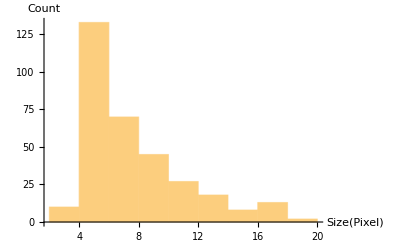

```mathematica
Histogram[pores[[All,2]][[All,2]],AxesLabel->{"Size(Pixel)","Count"}]
```

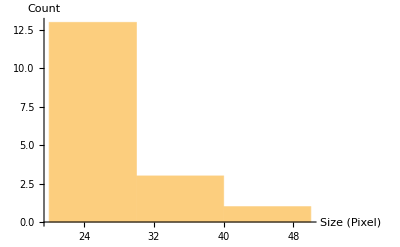

```mathematica
Histogram[pores1[[All,2]][[All,2]],AxesLabel->{"Size (Pixel)","Count"}]
```